```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/s1220054/Dissertation/Dissertation/DiSamp/src

```mathematica
y = 0.0001/(x(x-1))
```

0.0001/((-1+x) x)

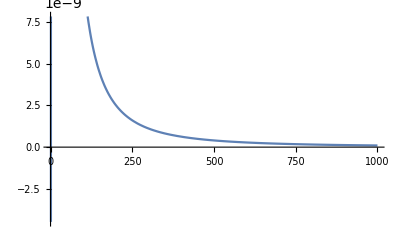

```mathematica
Plot[y,{x,0,1000}]
```

```mathematica
chidata =Import["chi.txt", "CSV"]
```

{{1,326},{2,458},{3,846},{4,961},{5,1193},{6,1154},{7,1181},{8,939},{9,1028},{10,698},{11,555},{12,271},{13,150},{14,152},{15,68},{16,13},{17,7},{18,0},{19,0},{20,0},{21,0},{22,0},{23,0},{24,0},{25,0},{26,0},{27,0},{28,0},{29,0},{30,0},{31,0},{32,0},{33,0},{34,0},{35,0},{36,0},{37,0},{38,0},{39,0},{40,0},{41,0},{42,0},{43,0},{44,0},{45,0},{46,0},{47,0},{48,0},{49,0},{50,0},{51,0},{52,0},{53,0},{54,0},{55,0},{56,0},{57,0},{58,0},{59,0},{60,0},{61,0},{62,0},{63,0},{64,0},{65,0},{66,0},{67,0},{68,0},{69,0},{70,0},{71,0},{72,0},{73,0},{74,0},{75,0},{76,0},{77,0},9845,{9923,0},{9924,0},{9925,0},{9926,0},{9927,0},{9928,0},{9929,0},{9930,0},{9931,0},{9932,0},{9933,0},{9934,0},{9935,0},{9936,0},{9937,0},{9938,0},{9939,0},{9940,0},{9941,0},{9942,0},{9943,0},{9944,0},{9945,0},{9946,0},{9947,0},{9948,0},{9949,0},{9950,0},{9951,0},{9952,0},{9953,0},{9954,0},{9955,0},{9956,0},{9957,0},{9958,0},{9959,0},{9960,0},{9961,0},{9962,0},{9963,0},{9964,0},{9965,0},{9966,0},{9967,0},{9968,0},{9969,0},{9970,0},{9971,0},{9972,0},{9973,0},{9974,0},{9975,0},{9976,0},{9977,0},{9978,0},{9979,0},{9980,0},{9981,0},{9982,0},{9983,0},{9984,0},{9985,0},{9986,0},{9987,0},{9988,0},{9989,0},{9990,0},{9991,0},{9992,0},{9993,0},{9994,0},{9995,0},{9996,0},{9997,0},{9998,0},{9999,0}}
 |  |  |  |

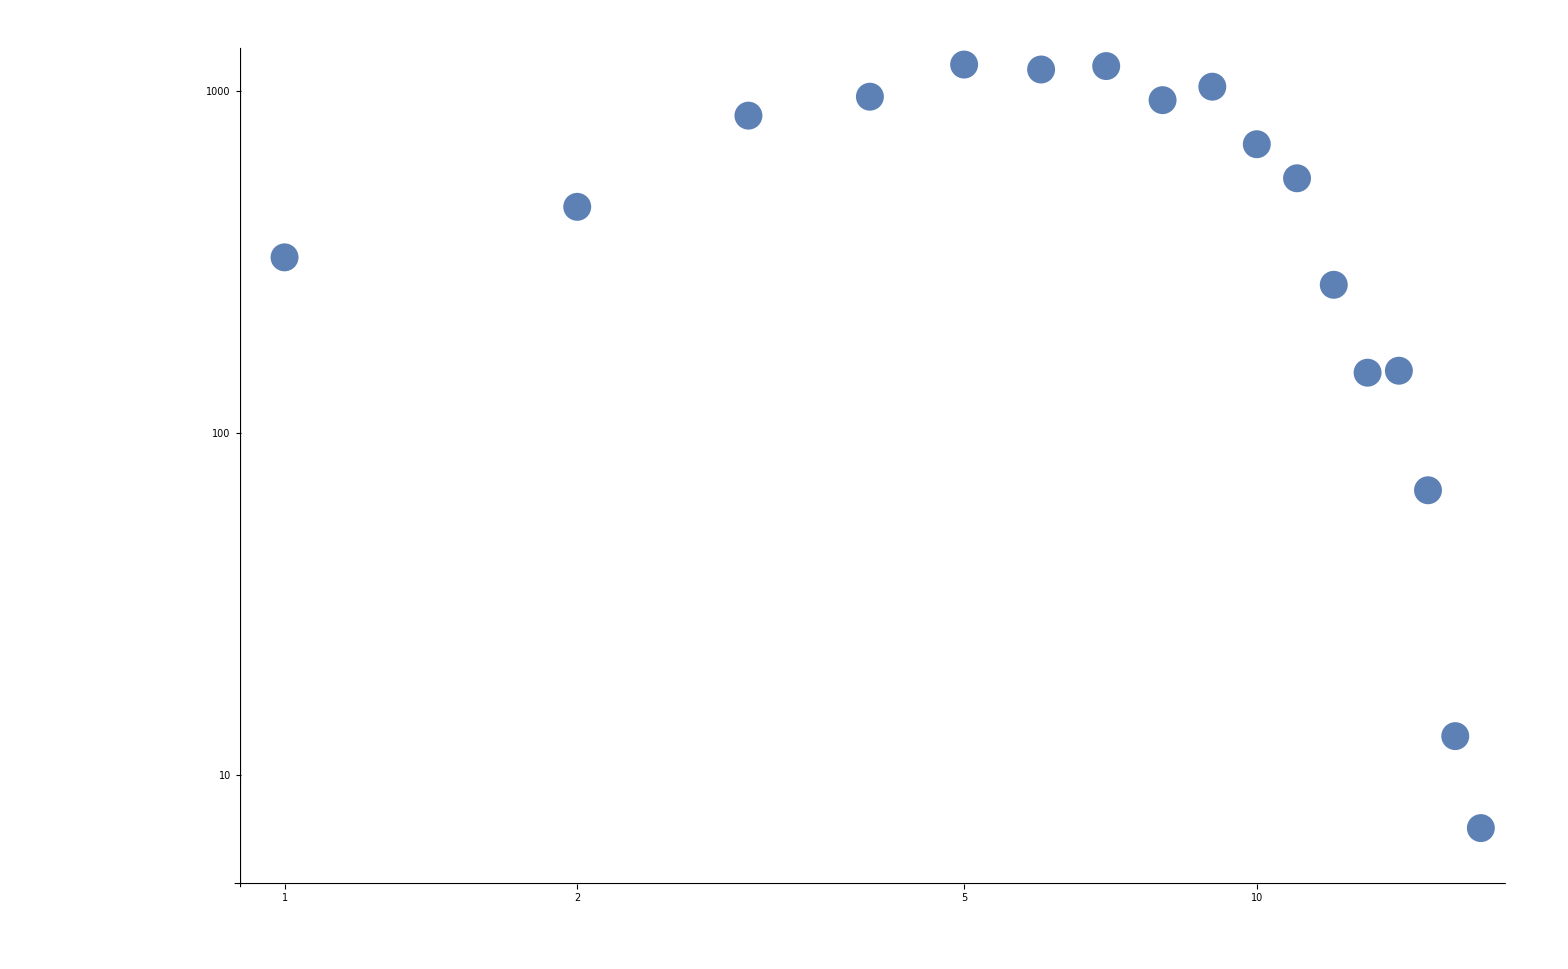

```mathematica
ListLogLogPlot[{chidata},PlotRange->All]
```

```mathematica
datanew=Import["array.txt", "CSV"]
```

{1}
 |  |  |  |

```mathematica
ArrayPlot[datanew, ColorFunction->"Rainbow"]
```

-Graphics-

```mathematica
chinewdata = Import["chinew.txt", "CSV"]
```

{{0,1},{1,3258},{2,1338},{3,715},{4,463},{5,339},{6,276},{7,201},{8,162},{9,148},{10,119},{11,114},{12,101},{13,101},{14,85},{15,73},{16,76},{17,49},{18,53},{19,53},{20,42},{21,52},{22,32},{23,38},{24,41},{25,27},{26,35},{27,23},{28,33},{29,28},{30,29},{31,28},{32,24},{33,22},{34,22},{35,20},{36,18},{37,16},{38,15},{39,12},{40,20},{41,19},{42,15},{43,11},{44,14},{45,17},{46,18},{47,17},{48,11},{49,9},{50,13},{51,12},{52,14},{53,12},{54,8},{55,8},{56,14},{57,11},{58,7},{59,8},{60,12},{61,14},{62,12},{63,7},{64,6},{65,7},{66,5},{67,12},{68,5},{69,7},{70,8},{71,12},{72,8},{73,6},{74,8},9851,{9926,0},{9927,0},{9928,0},{9929,0},{9930,0},{9931,0},{9932,0},{9933,0},{9934,0},{9935,0},{9936,0},{9937,0},{9938,0},{9939,0},{9940,0},{9941,0},{9942,0},{9943,0},{9944,0},{9945,0},{9946,0},{9947,0},{9948,0},{9949,0},{9950,0},{9951,1},{9952,0},{9953,0},{9954,0},{9955,0},{9956,0},{9957,0},{9958,0},{9959,0},{9960,0},{9961,0},{9962,0},{9963,0},{9964,0},{9965,0},{9966,0},{9967,0},{9968,0},{9969,0},{9970,0},{9971,0},{9972,0},{9973,0},{9974,0},{9975,0},{9976,0},{9977,0},{9978,0},{9979,0},{9980,0},{9981,0},{9982,0},{9983,0},{9984,0},{9985,0},{9986,0},{9987,0},{9988,0},{9989,0},{9990,0},{9991,0},{9992,0},{9993,0},{9994,0},{9995,0},{9996,0},{9997,0},{9998,0},{9999,0},{10000,0}}
 |  |  |  |

```mathematica
dataacc=chinewdata;
dataacc[[All,#2]]=Accumulate[chinewdata[All,#2]]
```

Set::pkspec1: The expression #2 cannot be used as a part specification.

{{0,1},{1,3258},{2,1338},{3,715},{4,463},{5,339},{6,276},{7,201},{8,162},{9,148},{10,119},{11,114},{12,101},{13,101},{14,85},{15,73},{16,76},{17,49},{18,53},{19,53},{20,42},{21,52},{22,32},{23,38},{24,41},{25,27},{26,35},{27,23},{28,33},{29,28},{30,29},{31,28},{32,24},{33,22},{34,22},{35,20},{36,18},{37,16},{38,15},{39,12},{40,20},{41,19},{42,15},{43,11},{44,14},{45,17},{46,18},{47,17},{48,11},{49,9},{50,13},{51,12},{52,14},{53,12},{54,8},{55,8},{56,14},{57,11},{58,7},{59,8},{60,12},{61,14},{62,12},{63,7},{64,6},{65,7},{66,5},{67,12},{68,5},{69,7},{70,8},{71,12},{72,8},{73,6},9853,{9927,0},{9928,0},{9929,0},{9930,0},{9931,0},{9932,0},{9933,0},{9934,0},{9935,0},{9936,0},{9937,0},{9938,0},{9939,0},{9940,0},{9941,0},{9942,0},{9943,0},{9944,0},{9945,0},{9946,0},{9947,0},{9948,0},{9949,0},{9950,0},{9951,1},{9952,0},{9953,0},{9954,0},{9955,0},{9956,0},{9957,0},{9958,0},{9959,0},{9960,0},{9961,0},{9962,0},{9963,0},{9964,0},{9965,0},{9966,0},{9967,0},{9968,0},{9969,0},{9970,0},{9971,0},{9972,0},{9973,0},{9974,0},{9975,0},{9976,0},{9977,0},{9978,0},{9979,0},{9980,0},{9981,0},{9982,0},{9983,0},{9984,0},{9985,0},{9986,0},{9987,0},{9988,0},{9989,0},{9990,0},{9991,0},{9992,0},{9993,0},{9994,0},{9995,0},{9996,0},{9997,0},{9998,0},{9999,0},{10000,0}}[All,1]
 |  |  |  |

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Symbol[]

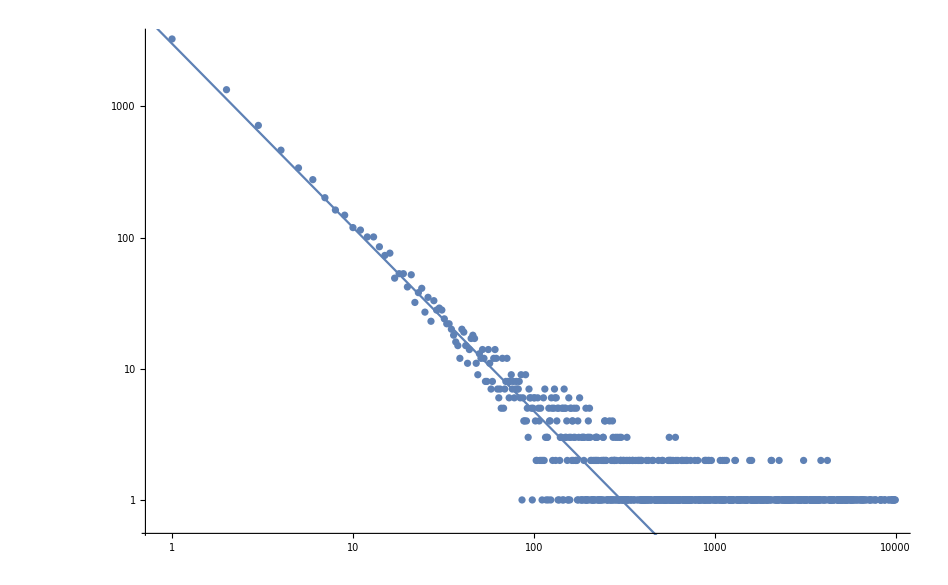

```mathematica
Show[ListLogLogPlot[{chinewdata},PlotRange->All],LogLogPlot[3000/(x^1.4),{x,0.5,1000}]]
```